## Subradiance-protected excitation spreading for collimated photon emission

P. Huft
See paper by K. Ballantine, J. Ruostekoski

## notes

### Questions

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

Restricting this problem to the single-excitation subspace, the Hamiltonian matrix elements are: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), ℏ=1, where μ,ν specify polarization in a spherical basis and j,k are the atom indices in the 2D grid. The dynamics in this subspace are coherent, but H is non-Hermitian, so there is dissipation as the excitation diffuses into the collective ground state.

- Δ,γ values used are arbitrary with the given choice of plot units.

## general setup - run first

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*PHYSICAL CONSTANTS*)
ℏ = 6.62607015*^-34/(2π);
kB = 1.380649*^-23;
SetDirectory[NotebookDirectory[]];
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
λ = 7.8*10^-7;
k=2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ϵ0); (*single two-level atom linewidth, ℏ=1*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
atomnum = atomnum;(*Hamiltonian shape is atomnum x atomnum, with state vector = atomnum*)

(*FUNCTIONS*)
StepsTable[stepList_,list_]:=MapThread[{#1,#2}&,{stepList,list}];
unit[v_]:=v/(√(v.v));
GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));(*r is the positional unit vector, p is an atomic dipole moment*)
Subscript[e, μ_] :={{1,0,0},{0,1,0},{0,0,1}}[[μ]];(*generic basis vector set*)
Subscript[ecart, μ_]:={1/(√2){1,0,-1}, -ⅈ/(√2){1, 0, 1}, {0, 1,0}}[[μ]];
linewidthplot[sln_,polmodes_,gridshape_, numx_,numy_,plttitle_,saveplot_,savesoln_]:=Module[
{plots={},lastmode=0,modelist,plt,fname,title},
For[polmode=1,polmode<Length[polmodes]+1,polmode++,
modelist=polmodes[[polmode,2]];
For[i=1,i<Length[modelist]+1,i++,
AppendTo[plots,ListPlot[sln[[i+lastmode]],PlotRange->{-5,3},PlotStyle->modelist[[i,3]],Joined->True,PlotLegends-> {modelist[[i,2]]}]] ;
];
lastmode=i-1;
];
If[gridshape=="square",AppendTo[plots,Plot[Log10[3/(4π d^2)],{d,0.02,1.21},PlotStyle->Directive[Red,Dashed],PlotLegends->{"N→∞, In-plane"}]]];
title = If[plttitle=="",ToString[StringForm["Collective linewidths for ``x`` `` grid",numx,numy,gridshape]],plttitle];
plt = Show[plots,PlotLabel->Style[title,FontSize-> 14],ImageSize->Medium,Frame-> {True,True,False,False},FrameLabel-> {"Lattice period d [λ]","Log_10(v_n/γ)"},Axes-> False,LabelStyle-> Directive[Black,FontSize-> 12] ];
fname = ToString[StringForm["plot_linewidth_v_period_````x``.png",gridshape,numx,numy]];
If[saveplot,Export[fname,plt]];
fname = ToString[StringForm["soln_linewidth_v_period_````x``.txt",gridshape,numx,numy]];
If[savesoln,Export[fname,ToString[sln]]];
plt
](*x,y,z in spherical basis*);

BuildEqSys[hamiltonian_,atoms_,center_,excitation_]:=Module[{ψ,ψ0,excitedIdcs,eqs,ics,tmax,sys},
(*For generating the Schrodinger eq system to be solved for time-evolution of a system with 9 excitations

arguments in order: matrix of dimensions √atoms x √atoms, the index of the central atom, a function which takes a number of excited atoms and returns a scalar list of that length*)

(*Build the initial array state and eqs to solve*)
ψ = Array[Subscript[P, #][t]&,atoms];
ψ0 = ConstantArray[0,atoms];
excitedIdcs = Flatten@Table[center+i+j,{i,{-√atoms,0,√atoms}},{j,{-1,0,1}}];
ψ0[[excitedIdcs]]=excitation[Length[excitedIdcs]];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<atoms+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,ψ0,sys,excitedIdcs}
];
```

## linewidths vs lattice spacing

Set atomnums, run one of the grid geometry cells below, then run the “run” cell.

```mathematica
atomnumx = 31;(*only x value will be used to build square grid*)
atomnumy = Floor[2/(√3)atomnumx];(*used for hex lattices*)
{atomnumx,atomnumy}
```

{31,35}

#### square lattice setup

```mathematica
gridname= "square";
atomnumy=atomnumx;
atomnum = atomnumx*atomnumy;
fmode =unit[Flatten@Array[1&,atomnum]];
(*ferromagnetic state: all atoms with same polarization, in phase. can be used for either in-plane or out-of-plane basis*)
afmode =unit[Flatten@Array[(-1)^#&,atomnum]];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
xmodes = {Subscript[e, 1],{{fmode,"Symmetric",Blue},{afmode,"Antisymmetric",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane symmetric",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes}; 
idx[i_,j_,n_]:=(i-1)n+j//Simplify; (*get 1D atom idx from 2D coordinate indices*)
Subscript[r, i_,j_]:={0,Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->√atomnum;(*vector between atoms i,j in units lattice spacing*)
```

#### hexagonal lattice setup

```mathematica
atomnumy = atomnumx;
gridname = "hex";
atomnum = atomnumx atomnumy;
fmode =unit[Flatten@Array[1&,atomnumx atomnumy]];
afrowsmode = unit[Flatten@Array[(-1)^# Array[1&,atomnumx]&,atomnumy]];
afcolsmode = unit[Flatten@Array[(-1)^# Array[1&,atomnumy]&,atomnumx ]];
(*ferromagnetic state: all atoms with same polarization, in phase. can be used for either in-plane or out-of-plane basis*)
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afrowsmode,"A.F. rows",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes}; 
Subscript[r, i_,j_]:={0,Mod[j-1,atomnumx]-Mod[i-1,atomnumx]+1/2(Mod[Floor[(j-1)/atomnumx],2]-Mod[Floor[(i-1)/atomnumx],2]),(√3)/2(Floor[(j-1)/atomnumx]-Floor[(i-1)/atomnumx])};(*vector between atoms i,j in units lattice spacing*)
```

#### run

find the lattice period dependent transition linewidth for modes defined above.

```mathematica
soln=Array[{}&,Sum[Length[polarizationmodes[[n,2]]],{n,Length[polarizationmodes]}]];
lastmode =0;
runtime = Timing[
For[polmode=1,polmode<Length[polarizationmodes]+1,polmode++,
e[ν_]=polarizationmodes[[polmode,1]];
modelist = polarizationmodes[[polmode,2]];
For[d=0.01,d<1.26,d=d+0.05,(*loop over fractional lattice period*)
(*build the Hamiltonian*)
Hfull = Array[Subscript[H, ##]&,{atomnum,atomnum}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=d λ Subscript[r, i,j];
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hfull[[i,j]]=  (Ωij+ⅈ γij);
];
];
(*find the eigenmode overlap with modes of interest*)
{evals,evecs} = Eigensystem[Hfull];
For[mode=1,mode<Length[modelist]+1,mode++,
overlap = {};
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[modelist[[mode,1]].evecs[[i]]]}]
];
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
v= Im[evals[[maxIdx]]];(*mode linewidth*)
AppendTo[soln[[mode+lastmode]],{d,Log10[v/γ]}];
];(*end mode loop*)
];(*end d loop*)
lastmode=mode-1;(*since mode will increment just before the loop exits*)
];(*end pol loop*)
][[1]];
StringForm["Simulation took `` minutes",runtime/60//N]
```

Simulation took 0.172917 minutes

#### soln analysis

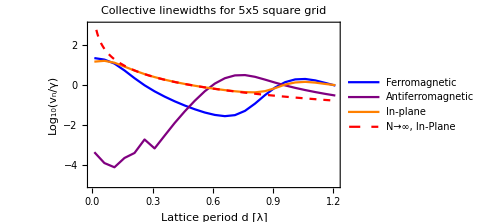

```mathematica
saveplt = False;
savesln = False;
linewidthplot[soln,polarizationmodes,gridname,atomnumx,atomnumy,"",saveplt,savesln]
```

```mathematica
atomnumy
```

5

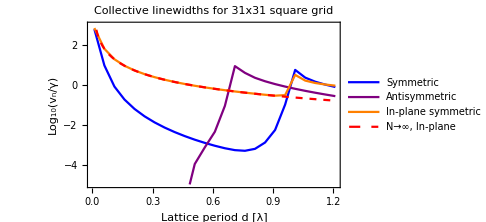

```mathematica
sqsoln = ToExpression[Import["soln_linewidth_v_period_sq31x31.txt"]];
saveplt = True;
savesln = False;
linewidthplot[sqsoln,polarizationmodes,gridname,atomnumx,atomnumy,"",saveplt,savesln]
```

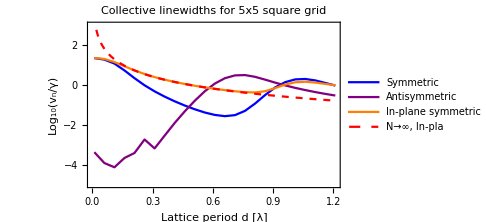

compare square and hex grids

```mathematica
(*hexsoln = ToExpression[Import["soln_linewidth_v_period_hex5x6.txt"]];*)
hexsoln = ToExpression[Import["soln_linewidth_v_period_hex5x5.txt"]];
sqsoln = ToExpression[Import["soln_linewidth_v_period_square5x5.txt"]];
```

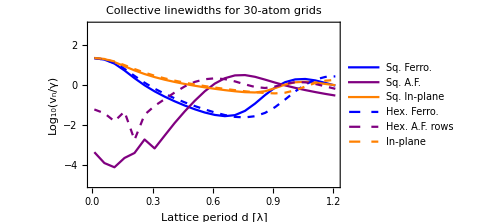

```mathematica
sln = Catenate[{sqsoln[[1;;3]],hexsoln}];
modes = {{None,{{None,"Sq. Ferro.",Blue},{None,"Sq. A.F.",Purple},{None,"Sq. In-plane",Orange},{None,"Hex. Ferro.",Directive[Blue,Dashed]},{None,"Hex. A.F. rows",Directive[Purple,Dashed]},{None, "In-plane",Directive[Orange,Dashed]}}}};
plt=linewidthplot[sln,modes,"",atomnumx,atomnumy,"Collective linewidths for 30-atom grids",False,False]
```

```mathematica
Export["linewidth_v_period_exactly30atoms_sq_hex.png",plt]
```

linewidth_v_period_exactly30atoms_sq_hex.png

```mathematica
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afrowsmode,"A.F. rows",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes};
```

```mathematica
Manipulate[ListPlot[Re[evecs[[i]]],PlotStyle-> {{0,25},{-.5,.5}}],{i,Range[Length[evecs]]}]
```

Part::partd: Part specification evecs⟦1⟧ is longer than depth of object.

ListPlot::lpn: Re[evecs⟦1⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification evecs⟦1⟧ is longer than depth of object.

ListPlot::lpn: Re[evecs⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification evecs⟦1⟧ is longer than depth of object.

ListPlot::lpn: Re[evecs⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification evecs⟦1⟧ is longer than depth of object.

ListPlot::lpn: Re[evecs⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification evecs⟦1⟧ is longer than depth of object.

ListPlot::lpn: Re[evecs⟦1⟧] is not a list of numbers or pairs of numbers.

## time evolution and defects

Run cells in order: lattice setup, either f- or afmode, build hamiltonian, add noise (optional), run.

```mathematica
atomnum =5^2;
γ=1;
(*easier to solve system if everything is a few orders of magnitude from 1*)
```

### square lattice setup

```mathematica
gridname= "square";
fmode =unit[Flatten@Array[1&,atomnum]];
(*ferromagnetic state: all atoms with same polarization, in phase. can be used for either in-plane or out-of-plane basis*)
afmode =unit[Flatten@Array[(-1)^#&,atomnum]];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afmode,"Antiferromagnetic",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes}; 
idx[i_,j_,n_]:=(i-1)n+j//Simplify; (*get 1D atom idx from 2D coordinate indices*)
Subscript[r, i_,j_]:={0,Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->√atomnum;(*vector between atoms i,j in units lattice spacing*)
Subscript[r, i_]:={0,Mod[i-1,n],Floor[(i-1)/n]}/.n-> √atomnum;
centerIdx =Floor[√atomnum/2](√atomnum+1)+1 ; 
(*idx of the central atom*)
perimeterIdcs={Range[1,√atomnum],Range[atomnum-√atomnum+1,atomnum],Table[1+n √atomnum,{n,Range[0,√atomnum-1]}],Table[(1+n) √atomnum,{n,Range[0,√atomnum-1]}]};
centerRowIdcs = Table[centerIdx+i,{i,Range[(-√atomnum+1)/2,(√atomnum-1)/2]}];
```

### f-mode

```mathematica
d =0.75;
modename =  "ferromagnetic";
fmode =unit[Flatten@Array[1&,atomnum]];
mode = fmode;
initExcitation[numExcited_] := 1/√numExcited; (*excitation per atom*)
e[i_]:=Subscript[e, 1];
```

### af-mode

```mathematica
d =0.4;
modename="antiferromagnetic";
afmode =unit[Flatten@Array[(-1)^#&,atomnum]];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
mode = afmode;
initExcitation[numExcited_]:=Array[(1/√numExcited)(-1)^(#+1)&,numExcited]
e[i_]:=Subscript[e, 1];
```

### in-plane mode

```mathematica
d =0.75;
modename =  "inplane";
fmode =unit[Flatten@Array[1&,atomnum]];
mode = fmode;
initExcitation[numExcited_] := 1/√numExcited; (*excitation per atom*)
e[i_]:=Subscript[e, 3];
```

### build noise-free Hamiltonian, find target eigenmode

```mathematica
(*Build the noise-free Hamiltonian then find the well-defined target eigenmode*)
Hfull= Array[Subscript[H, ##]&,{atomnum,atomnum}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=d λ (Subscript[r, j]-Subscript[r, i]);
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hfull[[i,j]]=  Ωij+ⅈ γij;
];
];
(*Find the target eigenmode*)
overlap = {};
{evals,evecs} = Eigensystem[Hfull];
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[mode.evecs[[i]]]}]
];
modeIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
targetMode = evecs[[modeIdx]];
```

### run - ideal case

```mathematica
(*generate the Schrodinger eq system then solve*)
tmax=800/γ;
{ψ,ψ0,eqSys,excitedIdcs} = BuildEqSys[Hfull,atomnum,centerIdx,initExcitation];
{time,soln}= Timing[First@NDSolve[eqSys, ψ, {t,0,tmax},AccuracyGoal->15,PrecisionGoal->10,Method-> "ExplicitRungeKutta"]];
soln = Table[soln[[i,2]],{i,Range[atomnum]}];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
```

NDSolve::ndstf: At t == 65.1073, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

Time to run sim: 0 mins

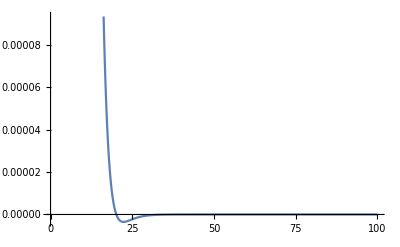

```mathematica
Plot[Re[soln[[centerIdx]]],{t,0,100}]
```

### run - noise and defects

#### polarization defects

what is typical polarization spread after a Glenn-Taylor polarizer?

#### positional variance

```mathematica
avgs = 10; (*number of averages*)
```

```mathematica
e[i_]:={1,0,0};
avgs = 20; (*number of averages*)
stdSteps = {10^-4,5*^-3,10^-3,5*^-2,10^-2,.5,.1}; 
(*trap depth steps*)
modes = {{fmode,0.75,"Ferromagnetic"},{afmode,0.4,"A.F."}};
solnList = Array[{}&,Length[modes]];
(*soln={};*)(*tuples: {depth,Log10[linewidth/γ]}*)
time=Timing[
For[midx=1,midx<Length[modes]+1,midx++,
For[didx=1,didx<Length[stdSteps]+1,didx++,
σ =stdSteps[[didx]]λ;
evalAvg=0;
For [step=0,step<avgs,step++,

(*generate positional noise*)
rNoise = Array[{RandomVariate[NormalDistribution[0,σ]],RandomVariate[NormalDistribution[0,σ]],RandomVariate[NormalDistribution[0,σ]]}&,atomnum];
ΔrNoise = Table[rNoise[[j]]-rNoise[[i]],{i,Range[atomnum]},{j,Range[atomnum]}];

(*construct the Hamiltonian with noise*)
Hnoisy= Array[Subscript[H, ##]&,{atomnum,atomnum}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=modes[[midx,2]] λ (Subscript[r, j]-Subscript[r, i])+ΔrNoise[[j,i]];
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hnoisy[[i,j]]=  Ωij+ⅈ γij;
];
];
(*find linewidth of target mode*)
{evalsNoisy, evecsNoisy}=Eigensystem[Hnoisy];
overlap = {};
For[i = 1,i<Length[evecsNoisy]+1,i++,
AppendTo[overlap,{i,Abs[modes[[midx,1]].evecsNoisy[[i]]]}](**)
];
targetIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
evalAvg+=evalsNoisy[[targetIdx]]/avgs;
];
AppendTo[solnList[[midx]],{σ/λ,Log10[Im[evalAvg]/γ]}]
];
];
][[1]];
Print[ToString[StringForm["ran sim in `` mins",Floor[time/60//N]]]]
```

ran sim in 20 mins

```mathematica
Export[ToString[StringForm["soln_linewidth_v_trapdepth_``avgs_``x``_``.txt",avgs,√atomnum,√atomnum,gridname]],ToString[solnList]]
```

soln_linewidth_v_trapdepth_10avgs_11x11_square.txt

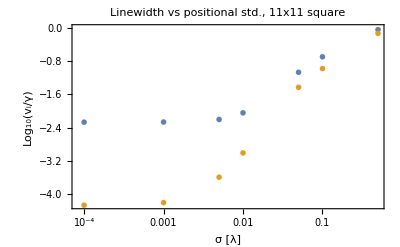

```mathematica
plt=ListLogLinearPlot[solnList,PlotMarkers->{{Red,5},{Blue,5}},PlotLegends-> {"Ferro.,d=0.75λ","A.F.,d=0.4λ"},PlotLabel-> StringForm["Linewidth vs positional std., ``x`` ``",√atomnum,√atomnum,gridname],Frame-> {True,True,False,False},FrameLabel-> {"σ [λ]","Log_10(v_i/γ)"},FrameTicks->Automatic, PlotRange-> All,Axes-> False,
LabelStyle-> Directive[Black, FontSize-> 12],ImageSize->400]
```

```mathematica
(*fname = ToString[StringForm["plot_linewidth_v_trapdepth_``avgs_``x``_``.png",avgs,√atomnum,√atomnum,gridname]];
Export[fname,plt]*)
```

plot_linewidth_v_trapdepth_10avgs_11x11_square.png

```mathematica
solnList = ToExpression[Import["soln_linewidth_v_trapdepth_10avgs_11x11_square.txt"]];
```

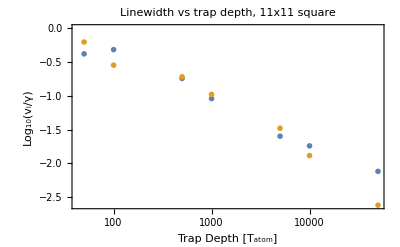

```mathematica
plt=ListLogLinearPlot[solnList,PlotMarkers->{{Red,5},{Blue,5}},PlotLegends-> {"Ferro.,d=0.75λ","A.F.,d=0.4λ"},PlotLabel-> StringForm["Linewidth vs trap depth, ``x`` ``",√atomnum,√atomnum,gridname],Frame-> {True,True,False,False},FrameLabel-> {"Trap Depth [T_atom]","Log_10(v_i/γ)"},FrameTicks->Automatic, PlotRange-> All,Axes-> False,
LabelStyle-> Directive[Black, FontSize-> 12],ImageSize->400]
```

```mathematica
Clear
```

```mathematica
a = {{1,2},{2,4}};
σz[depth_]:=w0/(2 √depth);
Table[{σz[a[[i,1]]],a[[i,2]]},{i,Range[Length[a]]}]
```

{{1/2000000,2},{1/(2000000 √2),4}}

```mathematica
a
```

{{1,2},{2,4}}

```mathematica
stdPtsList={};
For[i=1,i<Length[solnList]+1,i++,
pts = solnList[[i]];
stdPts = Table[{σz[pts[[j,1]]]/λ,pts[[j,2]]},{j,Range[Length[pts]]}];
AppendTo[stdPtsList,stdPts];
];
```

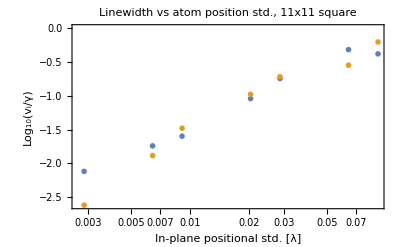

```mathematica
plt=ListLogLinearPlot[stdPtsList,PlotMarkers->{{Red,5},{Blue,5}},PlotLegends-> {"Ferro.,d=0.75λ","A.F.,d=0.4λ"},PlotLabel-> StringForm["Linewidth vs atom position std., ``x`` ``",√atomnum,√atomnum,gridname],Frame-> {True,True,False,False},FrameLabel-> {"In-plane positional std. [λ]","Log_10(v_i/γ)"},FrameTicks->Automatic, PlotRange-> All,Axes-> False,
LabelStyle-> Directive[Black, FontSize-> 12],ImageSize->400]
```

```mathematica
Export[ToString[StringForm["soln_linewidth_v_pos_std_``avgs_``x``_``.txt",avgs,√atomnum,√atomnum,gridname]],ToString[stdPtsList]]
```

soln_linewidth_v_pos_std_10avgs_11x11_square.txt

```mathematica
Export[ToString[StringForm["plot_linewidth_v_pos_std_``avgs_``x``_``.png",avgs,√atomnum,√atomnum,gridname]],plt]
```

plot_linewidth_v_pos_std_10avgs_11x11_square.png

#### imperfect array filling

```mathematica
fillSteps = Range[0.3,1,0.1]; (*grid filling if defects*)
avgs = 10; (*number of averages*)
e[i_]:={1,0,0};
avgs = 50; (*number of averages*) 
(*trap depth steps*)
modes = {{fmode,0.75,"Ferromagnetic"},{afmode,0.4,"A.F."}};
```

```mathematica
solnList = Array[{}&,Length[modes]];
(*soln={};*)(*tuples: {depth,Log10[linewidth/γ]}*)
time=Timing[
For[midx=1,midx<Length[modes]+1,midx++,
For[fidx=1,fidx<Length[fillSteps]+1,fidx++,
filling =fillSteps[[fidx]]; 
defects=atomnum-Floor[filling atomnum+0.5];

evalAvg=0;
For [step=0,step<avgs,step++,
(*remove some atoms from the system*)
atomIcds = Range[atomnum];
For[i=0,i<defects,i++,
rand = RandomChoice[atomIcds];
atomIcds= Select[atomIcds,#≠rand&];
];
atoms=Length[atomIcds];

(*construct the Hamiltonian with noise*)
Hnoisy= Array[Subscript[H, ##]&,{atoms,atoms}];
For[i=1,i<atoms+1,i++,
For[j=1,j<atoms+1,j++,
u=modes[[midx,2]] λ (Subscript[r, atomIcds[[j]]]-Subscript[r, atomIcds[[i]]]);
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hnoisy[[i,j]]=  Ωij+ⅈ γij;
];
];
(*find linewidth of target mode*)
{evalsNoisy, evecsNoisy}=Eigensystem[Hnoisy];
overlap = {};
For[i = 1,i<Length[evecsNoisy]+1,i++,
AppendTo[overlap,{i,Abs[modes[[midx,1]][[;;atoms]].evecsNoisy[[i]]]}]
];
targetIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
evalAvg+=evalsNoisy[[targetIdx]]/avgs;
If[filling==1,
{evalAvg*=avgs;
Break[]}
];
];
AppendTo[solnList[[midx]],{filling,Log10[Im[evalAvg]/γ]}]
];
];
][[1]];
Print[ToString[StringForm["ran sim in `` mins",Floor[time/60//N]]]]
```

ran sim in 32 mins

```mathematica
(*Export[ToString[StringForm["soln_linewidth_v_filling_higheff_``avgs_``x``_``.txt",avgs,√atomnum,√atomnum,gridname]],ToString[solnList]]*)
```

soln_linewidth_v_filling_higheff_30avgs_11x11_square.txt

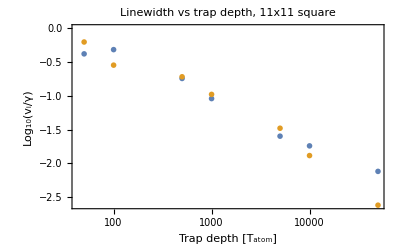

```mathematica
plt=ListLogLinearPlot[solnList,PlotMarkers->{{Red,5},{Blue,5}},PlotLegends-> {"Ferro.,d=0.75λ","A.F.,d=0.4λ"},PlotLabel-> StringForm["Linewidth vs array filling, ``x`` ``",√atomnum,√atomnum,gridname],Frame-> {True,True,False,False},FrameLabel-> {"Array Filling Efficiency","Log_10(v_i/γ)"},FrameTicks->Automatic, PlotRange-> All,Axes-> False,
LabelStyle-> Directive[Black, FontSize-> 12],ImageSize->400]
```

Replace trap depth index with corresponding in-plane positional std in units λ

```mathematica
(*Export[ToString[StringForm["plot_linewidth_v_filling_higheff_``avgs_``x``_``.png",avgs,√atomnum,√atomnum,gridname]],plt]*)
```

plot_linewidth_v_filling_higheff_small_30avgs_11x11_square.png

#### positional variance - time evol

average over solutions where atoms have Boltzmann positional variance. assume gaussian beam dipole traps.

```mathematica
w0=1*^-6;(*trap waist [m]*)
depth =1000; (*trap depth as multiple of the atom temperature*)
zR = π w0^2/λ;
"in-plane positional std / λ"
σy =σz= 1/2 w0/√depth;
σy/λ//N
"out-of-plane positional std / λ"
σx=zR/√(2 depth);
σx/λ//N
```

in-plane positional std / λ

0.020271

out-of-plane positional std / λ

0.115464

```mathematica
tmax=100/γ;(*max timestep; starts at 0*)
avgs = 10; (*number of averages*)
solnSum = Array[0&,atomnum];
For [step=0,step<avgs,step++,
(*generate noise*)
rNoise = Array[{RandomVariate[NormalDistribution[0,σx]],RandomVariate[NormalDistribution[0,σy]],RandomVariate[NormalDistribution[0,σz]]}&,atomnum];
ΔrNoise = Table[rNoise[[j]]-rNoise[[i]],{i,Range[atomnum]},{j,Range[atomnum]}];
(*construct the Hamiltonian with noise*)
Hnoisy= Array[Subscript[H, ##]&,{atomnum,atomnum}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=d λ (Subscript[r, j]-Subscript[r, i])+ΔrNoise[[j,i]];
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hnoisy[[i,j]]=  Ωij+ⅈ γij;
];
];
(*solve the system over specified time domain*)
{ψ,ψ0,eqSys,excitedIdcs} = BuildEqSys[Hnoisy,atomnum,centerIdx,initExcitation];
{time,soln}= Timing[First@NDSolve[eqSys, ψ, {t,0,tmax},AccuracyGoal->15,PrecisionGoal->10,Method-> Automatic]];
solnSum+=Table[soln[[i,2]],{i,Range[atomnum]}];
Print[ToString[StringForm["ran step `` in `` mins",step,Floor[time/60//N]]]]
]
soln = solnSum /avgs;
```

ran step 0 in 0 mins

ran step 1 in 0 mins

ran step 2 in 0 mins

ran step 3 in 0 mins

ran step 4 in 0 mins

ran step 5 in 0 mins

ran step 6 in 0 mins

ran step 7 in 0 mins

ran step 8 in 0 mins

ran step 9 in 0 mins

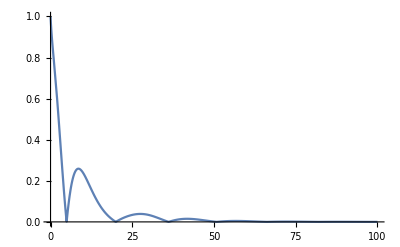

```mathematica
Plot[Abs[Re[avgSoln[[centerIdx]]]],{t,0,100},PlotRange->All]
```

```mathematica
StringForm["ran step `` in `` mins",step,If[time>60,time/60,Floor[time/60//N]]]
```

ran step 2 in 0 mins

### ideal soln analysis

#### ring down

Plot the excitation in the x polarization state for the initially excited atoms

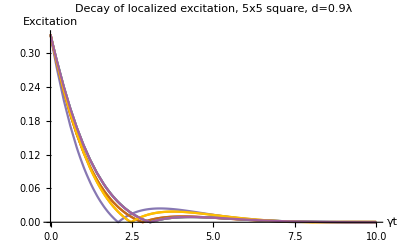

```mathematica
plt = Plot[Evaluate[Table[Abs[Re[soln[[i]]]],{i,excitedIdcs}]],{t,0,10},PlotRange->All, PlotLabel->Style[ StringForm["Decay of localized excitation, ``x`` ``, d=``λ",√atomnum,√atomnum,gridname,d],FontSize->14,Black],AxesLabel->{"γt","Excitation"},LabelStyle->Directive[Black, FontSize->12]]
```

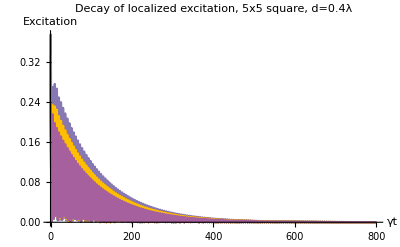

```mathematica
fname = ToString[StringForm["plot_excitation_decay_fmode_``x``_``.png",√atomnum,√atomnum,gridname]];
Export[fname,plt]
```

plot_excitation_decay_afmode_11x11_square.png

Same as above but varying the atoms of interest

```mathematica
Range[-2,2]
```

{-2,-1,0,1,2}

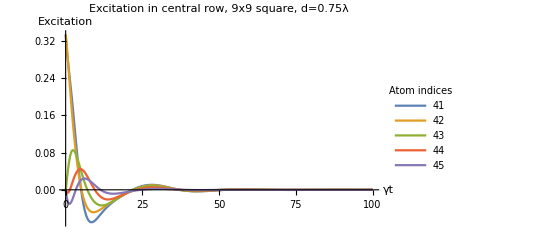

```mathematica
inner25Idcs =Flatten@Table[centerIdx+i+j,{i,{-2 √atomnum,-√atomnum,0,√atomnum,2 √atomnum}},{j,Range[-2,2]}];
outer16Idcs = Select[inner25Idcs,MemberQ[excitedIdcs,#]&];
sliceIdcs = Range[centerIdx,centerIdx+(√atomnum-1)/2];
plt = Plot[Evaluate[Table[Re[soln[[i]]],{i,sliceIdcs}]],{t,0,100},PlotRange->All, PlotLabel->Style[ StringForm["Excitation in central row, ``x`` ``, d=``λ",√atomnum,√atomnum,gridname,d],FontSize->14,Black],AxesLabel->{"γt","Excitation"},PlotLegends-> LineLegend[sliceIdcs,LegendLabel->"Atom indices"], LabelStyle->Directive[Black, FontSize->12]]
```

```mathematica
fname = ToString[StringForm["plot_excitation_decay_afmode_central_row_``x``_``.png",√atomnum,√atomnum,gridname]];
Export[fname,plt]
```

plot_excitation_decay_afmode_central_row_9x9_square.png

```mathematica
Clear[i]
```

```mathematica
({x,y,z}-Subscript[r, centerIdx,i])/.{i-> 1}
```

{x,y,z}

#### emission pattern

Plot the emitted field

```mathematica
scl = 1*^-6;
state[time_]:=soln[[;;]]/.t-> time;
atomfield[i_,x_,y_,z_,μ_,t_]:=state[t][[i]]GdotP[({x,y,z}scl-λ d Subscript[r, centerIdx,i] ),μ];
totalfieldXY[x_,z_,t_]:=Sum[({1/(√2),1/(√2),0}.atomfield[i,x,0.01,z,e[1],t]),{i,Range[atomnum]}];
totalfieldYZ[x0_,y_,z_,t_]:=Sum[({0,1/(√2),1/(√2)}.atomfield[i,x0,y,z,e[1],t]),{i,Range[atomnum]}];
fieldmax=Abs[atomfield[centerIdx,0,0.01,0,e[1],0].atomfield[centerIdx,0,0.01,0,e[1],0]];
atomDisksZ=Table[Graphics[{Red,Disk[λ d{ 0,Mod[i-1,√atomnum]-Subscript[r, centerIdx][[2]]}/scl,0.2 d λ/scl]}],{i,Range[√atomnum]},{j,Range[√atomnum]}];
atomDisksYZ=Table[Graphics[{Red,Disk[λ d({ Mod[i-1,√atomnum],Floor[(i-1)/√atomnum]}-Subscript[r, centerIdx][[2;;3]])/scl,0.2 d λ/scl]}],{i,Range[atomnum]}];
```

```mathematica
(*plot the field in the y-z plane at various time steps*)
tstep=γ;
x0 = 3;
zmax =5;
zmin = -zmax;
ymax =  zmax;
ymin = -ymax;
rangemax =2*^7; 
time=Timing[
dplt=Legended[DensityPlot[Abs[totalfieldYZ[x0,y,z,tstep]]^2/rangemax,{y,ymin,ymax},{z,ymin,ymax},ColorFunction->"SunsetColors",ColorFunctionScaling->{0,Abs[totalfieldYZ[x0,0,0,tstep]]^2/rangemax},PlotRange-> {0,rangemax},MaxRecursion->2,PlotPoints->100,FrameLabel->{"z [μm]","y [μm]"}],Placed[BarLegend[{"SunsetColors",{0,1}},LegendLayout->"Column"],{After,Center}]]
][[1]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60+0.5//N]]];
```

Time to run sim: 4 mins

```mathematica
plt=Show[dplt,atomDisksYZ,Frame-> True,FrameLabel->{"z [μm]","y [μm]"},PlotLabel-> Style[StringForm["          Emitted radiation |Ε|^2, t=``γ, ``x`` ``",tstep,√atomnum,√atomnum,gridname],Black,FontSize->14],LabelStyle-> Directive[Black,FontSize->12]]
```

-Graphics-

```mathematica
Export[ToString[StringForm["plot_emission_yz_``_t``gamma_x0``_``x``_``_``umx``um.png",modename,tstep/γ,x0,√atomnum,√atomnum,gridname,Floor[zmax-zmin],Floor[ymax-ymin]]],plt]
```

plot_emission_yz_inplane_t1gamma_x03_5x5_square_10umx10um.png

```mathematica
(*plot the field in the x-z plane at various time steps*)
tstep=4γ;
xmax =5;
xmin = -xmax;
ymax =  xmax;
ymin = -ymax;
rangemax =5*^8; 
time=Timing[
dplt=Legended[DensityPlot[Abs[totalfieldXY[x,z,tstep]]^2/rangemax,{x,xmin,xmax},{z,ymin,ymax},ColorFunction->"SunsetColors",ColorFunctionScaling->{0,Abs[totalfieldXY[0,0,tstep]]^2/rangemax},PlotRange-> {0,rangemax},MaxRecursion->2,PlotPoints->100,FrameLabel->{"x [μm]","y [μm]"}],Placed[BarLegend[{"SunsetColors",{0,1}},LegendLayout->"Column"],{After,Center}]]
][[1]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60+0.5//N]]];
```

Time to run sim: 2 mins

```mathematica
plt=Show[dplt,atomDisksZ,Frame-> True,FrameLabel->{"x [μm]","y [μm]"},PlotLabel-> Style[StringForm["          Emitted radiation |Ε|^2, t=``γ, ``x`` ``",tstep,√atomnum,√atomnum,gridname],Black,FontSize->14],LabelStyle-> Directive[Black,FontSize->12]]
```

-Graphics-

```mathematica
Export[ToString[StringForm["plot_emission_xz_``_t``gamma_``x``_``_``umx``um.png",modename,tstep/γ,√atomnum,√atomnum,gridname,Floor[xmax-xmin],Floor[ymax-ymin]]],plt]
```

plot_emission_xz_inplane_t4gamma_5x5_square_10umx10um.png

TODO: plot the emitted field from in-plane excitation at 3 μm axially from the atom plane

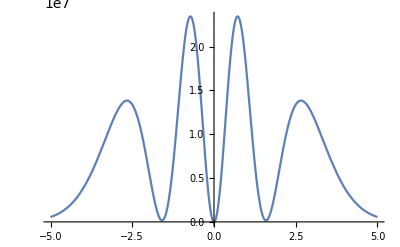

```mathematica
Plot[Abs[totalfieldYZ[x0,0,x,tstep]]^2,{x,-5,5},PlotRange->All]
```

```mathematica
fieldmax
```

4.07468×10^8

Try log plot without dictating the color scale

```mathematica
Export[ToString[StringForm["plot_log_emission_``_t``gamma_``x``_``_``umx``um.png",modename,tstep,√atomnum,√atomnum,gridname,Floor[xmax-xmin],Floor[ymax-ymin]]],plt]
```

plot_emission_inplane_t0gamma_5x5_square_10umx10um.png

```mathematica
atomDisks=Table[Graphics[{Red,Disk[λ d({Mod[i-1,√atomnum],Floor[(i-1)/√atomnum]}-{Subscript[r, centerIdx,i][[2]],Subscript[r, centerIdx,i][[3]]}),0.05 d λ]}],{i,Range[atomnum]}];
Show[intplot,atomDisks]
```

```mathematica
(*single dipole field as sanity check*)
xmax =5;
xmin = -xmax;
ymax =  xmax;
ymin = -ymax;
plt=Legended[DensityPlot[Abs[(Subscript[e, 1].atomfield[centerIdx,x,0.01,z,Subscript[e, 1],0])/fieldmax]^2,{x,xmin,xmax},{z,ymin,ymax},MaxRecursion->2,PlotPoints->100,ColorFunction->"SunsetColors",ColorFunctionScaling->{0,Abs[Subscript[e, 1].atomfield[centerIdx,1,0.01,1,Subscript[e, 1],0]]^2/Abs[Subscript[e, 1].atomfield[centerIdx,1,0.01,1,Subscript[e, 1],0]]^2},FrameLabel->{"x [μm]","y [μm]"}],Placed[BarLegend[{"SunsetColors",{0,1}},LegendLayout->"Column"],{After,Center}]]
```

-Graphics-

```mathematica
Export["single_dipole_efield_intensity.png",plt]
```

single_dipole_efield_intensity.png

#### decay and mode overlap

Get explicit lists of solution pts for plotting high-res time-domain results (specifically for the animations and field plot)

```mathematica
savesoln = False;
```

```mathematica
(*Get explicit points for the solution and transpose to get a state vector at each timestep*)
ti=0;numsteps=100;tf=(numsteps-1)/γ;
tsteps = Range[ti,tf,(tf-ti)/(numsteps-1)];
(*soln with rows i having Subscript[P, i] evaluated at each timestep t*)
solnPts = Table[Table[soln[[i]],{t,tsteps}],{i,Range[atomnum]}];

(*transpose soln to get a vector state at each tstep*)
vecSoln = Transpose@solnPts;
normL = Sum[Abs[evecs[[i]].vecSoln[[1]]]^2,{i,Range[atomnum]}];
modePts = Table[Abs[vecSoln[[t]].targetMode]^2/normL,{t,Range[numsteps]}];
(*can make the lines below more efficient by only computing the sums once*)
totalPts =  Table[Sum[Abs[vecSoln[[t]].evecs[[i]]]^2,{i,Range[atomnum]}]/normL,{t,Range[numsteps]}];
otherPts = Table[totalPts[[t]]-modePts[[t]],{t,Range[numsteps]}];
modeTuples= StepsTable[tsteps,modePts];(*fmode occupation at each time step*)
otherTuples = StepsTable[tsteps,otherPts];
totalTuples = StepsTable[tsteps,totalPts];
(*occupation in all other modes*)
```

```mathematica
fname = ToString[StringForm["soln_time_evol_``_``_````x``.txt",Floor[ti],Floor[tf],gridname,√atomnum,√atomnum]];
If[savesoln,Export[fname,ToString[solnPts]]];
```

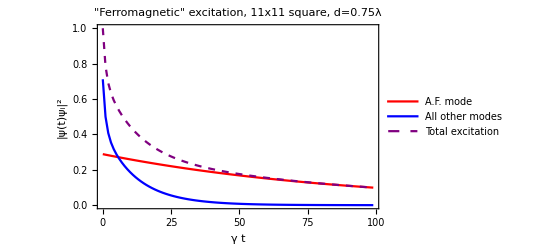

```mathematica
plt=ListPlot[{modeTuples,otherTuples,totalTuples},PlotRange->All,PlotStyle-> {Red,Blue,{Purple,Dashed}},PlotLabel->Style[StringForm["\"Ferromagnetic\" excitation, ``x`` ``, d=``λ",√atomnum,√atomnum,gridname,d],Black,FontSize->14], PlotLegends->{"A.F. mode","All other modes","Total excitation"},Frame-> {True,True,False,False},FrameLabel->{"γ t","|ψ(t)ψ_i|^2"},LabelStyle->Directive[Black, FontSize-> 12],Joined-> True]
```

```mathematica
fname = ToString[StringForm["plot_afmode_decay_``x``_``.png",√atomnum,√atomnum,gridname]];
Export[fname,plt]
```

plot_afmode_decay_11x11_square.png

```mathematica
ListPlot[Re[evecs[[modeIdx]]]]
```

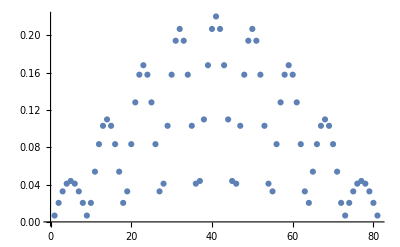

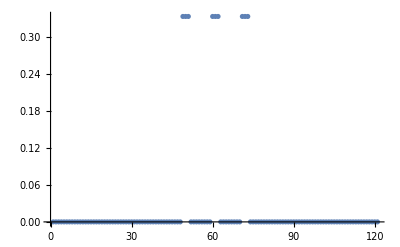

```mathematica
ListPlot[ψ0]
```

Scatter plot the eigenvalues vs mode occupation

```mathematica
modeEvalTuple = {{Log10[Im[evals[[modeIdx]]]], Abs[vecSoln[[1]].targetMode]^2/normL}};
otherEvalTuples = Table[{Log10[Im[evals[[i]]]],Abs[vecSoln[[1]].evecs[[i]]]^2/normL},{i,Select[Range[atomnum],(#≠modeIdx)&]}];
```

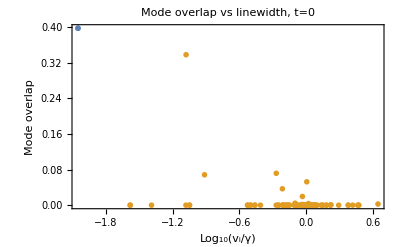

```mathematica
plt=ListPlot[{modeEvalTuple,otherEvalTuples},PlotMarkers->{{Red,7},{Blue,7}},PlotLegends-> {"Ferro. mode","Other modes"},PlotLabel-> "Mode overlap vs linewidth, t=0",Frame-> {True,True,False,False},FrameLabel-> {"Log_10(v_i/γ)","Mode overlap"},PlotRange-> All,Axes-> False,LabelStyle-> Directive[Black, FontSize-> 12]]
```

```mathematica
fname = ToString[StringForm["plot_overlap_v_linewidth_t0_fmode_``x``_``_9excited.png",√atomnum,√atomnum,gridname]];
Export[fname,plt]
```

plot_overlap_v_linewidth_t0_fmode_11x11_square_9excited.png

```mathematica
Select[Range[atomnum],(#≠modeIdx)&]
```

{1,3,4,5,6,7,8,9,10}

#### animation of polarization spreading

Make a movie of the excitation spreading. First redefine tsteps to get the desired resolution

```mathematica
(*Get explicit points for the solution and transpose to get a state vector at each timestep*)
(*savesoln = True;*)
ti=0;numsteps=100;tf=(numsteps-1)/γ;
tsteps = Range[ti,tf,(tf-ti)/(numsteps-1)];
(*soln with rows i having Subscript[ψ, i] evaluated at each timestep t*)
solnPts = Table[Table[soln[[i]],{t,tsteps}],{i,Range[atomnum]}];
(*fname = ToString[StringForm["soln_time_evol_``_``_````x``.txt",Floor[ti],Floor[tf],gridname,√atomnum,√atomnum]];
If[savesoln,Export[fname,ToString[solnPts]]];*)
(*transpose soln to get a vector state at each tstep*)
vecSoln = Transpose@solnPts;
{evals,evecs} = Eigensystem[Hfull];
normL = Sum[Abs[evecs[[i]].vecSoln[[1]]]^2,{i,Range[atomnum]}];
(*find the approximate ferromagnetic mode*)
overlap = {};
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[afmode.evecs[[i]]]}]
];
modeIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
mode = evecs[[modeIdx]];
fmodePts = Table[Abs[vecSoln[[t]].mode]^2/normL,{t,Range[numsteps]}];
(*can make the lines below more efficient by only computing the sums once*)
totalPts =  Table[Sum[Abs[vecSoln[[t]].evecs[[i]]]^2,{i,Range[atomnum]}]/normL,{t,Range[numsteps]}];
otherPts = Table[totalPts[[t]]-fmodePts[[t]],{t,Range[numsteps]}];
fmodeTuples= StepsTable[tsteps,fmodePts];(*fmode occupation at each time step*)
otherTuples = StepsTable[tsteps,otherPts];
totalTuples = StepsTable[tsteps,totalPts];
(*occupation in all other modes*)
```

```mathematica
gifSteps = Range[1,100];
normVecSoln = vecSoln*3;
cf [z_]:= Blend[{Purple,Black,Green},z];
(*colors="AvocadoColors";*)
```

```mathematica
cfData = Table[cf[i],{i,Range[0,1,0.1]}]
```

{RGBColor[0.5, 0., 0.5],RGBColor[0.4, 0., 0.4],RGBColor[0.3, 0., 0.3],RGBColor[0.19999999999999996, 0., 0.19999999999999996],RGBColor[0.09999999999999998, 0., 0.09999999999999998],RGBColor[0., 0., 0.],RGBColor[0., 0.20000000000000018, 0.],RGBColor[0., 0.40000000000000013, 0.],RGBColor[0., 0.6000000000000001, 0.],RGBColor[0., 0.8, 0.],RGBColor[0., 1., 0.]}

Make single frame plot of f,af eigenmodes:

```mathematica
overlap={};
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[fmode.evecs[[i]]]}]
];
modeIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
mode = evecs[[modeIdx]];
```

```mathematica
plt=Show[Legended[MatrixPlot[ArrayReshape[Re[evecs[[modeIdx]]],{√atomnum,√atomnum}],PlotLabel->Style[StringForm["Ferro. Eigenmode, ``x`` ``",√atomnum,√atomnum,gridname],Black,FontSize->14],Axes-> False,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{Range[1,√atomnum],Range[1,√atomnum]},ColorFunction->cf,ColorFunctionScaling->True],Placed[BarLegend[{cfData,{-1,1}},LegendLayout->"Column"],{After,Center}]]]
```

-Graphics-

```mathematica
fname = ToString[StringForm["plot_ferro_eigmode_``x``_``.png",√atomnum,√atomnum,gridname]];
Export[fname,plt]
```

plot_ferro_eigmode_11x11_square.png

Make gifs

```mathematica
Animate[Show[Legended[MatrixPlot[ArrayReshape[Re[normVecSoln[[i]]],{√atomnum,√atomnum}],PlotLabel->Style[StringForm["Excitation (P_x) spreading, ``x`` ``",√atomnum,√atomnum,gridname],Black,FontSize->14],Axes-> False,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{Range[1,√atomnum],Range[1,√atomnum]},ColorFunction->cf,ColorFunctionScaling->True],Placed[BarLegend[{cfData,{-1,1}},LegendLayout->"Column"],{After,Center}]],Graphics[Text[Style[ToString[StringForm["t=``/γ",Floor[tsteps[[i]]]]],White,Bold,FontSize->13],{10,0.5}]]],{i,gifSteps}]
```

```mathematica
Reverse[Range[1,√atomnum]]
```

{11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Style[ToString[StringForm["t=(``)/γ",100]],White]
```

```mathematica
(*gif = Table[Legended[MatrixPlot[ArrayReshape[Abs[Re[normVecSoln[[i]]]],{√atomnum,√atomnum}],PlotLabel->Style[StringForm["Excitation (|P_x|) spreading, ``x`` ``",√atomnum,√atomnum,gridname],Black,FontSize->14],Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{Range[1,√atomnum],Range[1,√atomnum]},ColorFunction->ColorData[cf],ColorFunctionScaling->False],Placed[BarLegend[{cf,{0,1}},LegendLayout->"Column"],{After,Center}]],{i,Range[100]}];*)
```

```mathematica
gif= Table[Show[Legended[MatrixPlot[ArrayReshape[Re[normVecSoln[[i]]],{√atomnum,√atomnum}],PlotLabel->Style[StringForm["Excitation (P_x) spreading, ``x`` ``",√atomnum,√atomnum,gridname],Black,FontSize->14],Axes-> False,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{Range[1,√atomnum],Range[1,√atomnum]},ColorFunction->cf,ColorFunctionScaling->True],Placed[BarLegend[{cfData,{-1,1}},LegendLayout->"Column"],{After,Center}]],Graphics[Text[Style[ToString[StringForm["t=``/γ",Floor[tsteps[[i]]]]],White,Bold,FontSize->13],{10,0.5}]]],{i,gifSteps}];
```

```mathematica
fname =ToString[StringForm["excitation_spreading_af_``x``_``.gif",√atomnum,√atomnum,gridname]];
Export[fname,gif,"DisplayDurations"->0.3 ]
```

excitation_spreading_af_11x11_square.gif

## misc physics analysis

#### Hamiltonian algebra

Try to get approximate analytical expressions for eigenvalues of square grid

```mathematica
Clear[k,λ,γ,d]
```

```mathematica
λ = (2π)/k;
(*vector between atoms i,j in units lattice spacing*)
atomnum =4; (*square grid*)
Subscript[r, i_,j_]:={0,Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->√atomnum;
e[i_]:= {1,0,0}; (*x-polarized*)
Hfull = Array[Subscript[H, ##]&,{atomnum,atomnum}];

For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=d λ Subscript[r, i,j];
Ωij=If[i==j,0,FullSimplify[(6 π γ)/k ComplexExpand[Re[e[i].GdotP[u,e[j]]]],Assumptions-> d∈Reals&&λ∈Reals ]] ;
γij=If[i==j,γ,FullSimplify[(6 π γ)/k ComplexExpand[Im[e[i].GdotP[u,e[j]]]],Assumptions-> d∈Reals&&λ∈Reals ]];
Hfull[[i,j]]= Ωij+ⅈ γij;
];
];
```

```mathematica
Hfull//MatrixForm
```

(ⅈ γ | (3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3) | (3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3) | (3 γ (√2 (-1+8 d^2 π^2) Cos[2 √2 d π]-4 d π Sin[2 √2 d π]))/(64 √(1/k^2) k π^3 Abs[d]^3)+(3 ⅈ γ Sign[d] (4 d π Cos[2 √2 d π]+√2 (-1+8 d^2 π^2) Sin[2 √2 d π]))/(64 π^3 Abs[d]^3)
(3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3) | ⅈ γ | (3 γ (√2 (-1+8 d^2 π^2) Cos[2 √2 d π]-4 d π Sin[2 √2 d π]))/(64 √(1/k^2) k π^3 Abs[d]^3)+(3 ⅈ γ Sign[d] (4 d π Cos[2 √2 d π]+√2 (-1+8 d^2 π^2) Sin[2 √2 d π]))/(64 π^3 Abs[d]^3) | (3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3)
(3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3) | (3 γ (√2 (-1+8 d^2 π^2) Cos[2 √2 d π]-4 d π Sin[2 √2 d π]))/(64 √(1/k^2) k π^3 Abs[d]^3)+(3 ⅈ γ Sign[d] (4 d π Cos[2 √2 d π]+√2 (-1+8 d^2 π^2) Sin[2 √2 d π]))/(64 π^3 Abs[d]^3) | ⅈ γ | (3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3)
(3 γ (√2 (-1+8 d^2 π^2) Cos[2 √2 d π]-4 d π Sin[2 √2 d π]))/(64 √(1/k^2) k π^3 Abs[d]^3)+(3 ⅈ γ Sign[d] (4 d π Cos[2 √2 d π]+√2 (-1+8 d^2 π^2) Sin[2 √2 d π]))/(64 π^3 Abs[d]^3) | (3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3) | (3 √(1/k^2) k γ ((-1+4 d^2 π^2) Cos[2 d π]-2 d π Sin[2 d π]))/(16 π^3 Abs[d]^3)+(ⅈ (6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π]))/(16 d^3 π^3) | ⅈ γ)

```mathematica
i=1;j=2;
u = d λ Subscript[r, i,j];
λ = (2π)/k;
FullSimplify[(6 π γ)/k ComplexExpand[Im[e[i].GdotP[u,e[j]]]],Assumptions-> d∈Reals&&λ∈Reals ]
```

(6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π])/(16 d^3 π^3)

```mathematica
FullSimplify[(6 π γ)/k ComplexExpand[Im[e[i].GdotP[u,e[j]]]],Assumptions-> d∈Reals&&λ∈Reals ]
```

(6 d π γ Cos[2 d π]+3 (-1+4 d^2 π^2) γ Sin[2 d π])/(16 d^3 π^3)

```mathematica
Hfull[[1,2]]
```

(6 π γ (Cos[√(d^2) k √(λ^2)]/(4 √(d^2) π √(λ^2))-(√(d^2) √(λ^2) Cos[√(d^2) k √(λ^2)])/(4 d^4 k^2 π λ^4)-Sin[√(d^2) k √(λ^2)]/(4 d^2 k π λ^2)))/k+(6 ⅈ π γ (Cos[√(d^2) k √(λ^2)]/(4 d^2 k π λ^2)+Sin[√(d^2) k √(λ^2)]/(4 √(d^2) π √(λ^2))-(√(d^2) √(λ^2) Sin[√(d^2) k √(λ^2)])/(4 d^4 k^2 π λ^4)))/k

```mathematica
e[1]
```

e[1]

#### Nearest neighbor terms

Why do the out-of-plane modes become very subradiant near λ = 0.7?

```mathematica
k=2π/λ;
```

Nearest- and next-to-nearest coupling terms:

```mathematica
Clear[k]
nn=ComplexExpand[Re[{1,0,0}.GdotP[{0,r,r},{1,0,0}]]]
```

```mathematica
1/(4π r)(Cos[√2 k r]/(√2)-Cos[√2 k √(r^2)]/(8 √2 k^2 r^2)-Sin[√2 k r]/(2 k π r))
```

```mathematica
nnn=ComplexExpand[Re[{1,0,0}.GdotP[{0,r,0},{1,0,0}]]]
```

```mathematica
1/(4 π r)(Cos[k r](1-1/(k^2 r^2))-Sin[k r]/(k r))
```

```mathematica
Collect[1/(4 π r)(Cos[k r](1-1/(k^2 r^2))-Sin[k r]/(k r))+1/(4π r)(Cos[√2 k r]/(√2)-Cos[√2 k r]/(8 √2 k^2 r^2)-Sin[√2 k r]/(2 k π r)),{1/(4π),1/r^2,1/r}]
```

((Cos[k r]+Cos[√2 k r]/(√2))/r+(-Cos[k r]/k^2-Cos[√2 k r]/(8 √2 k^2))/r^3+(-Sin[k r]/k-Sin[√2 k r]/(2 k π))/r^2)/(4 π)

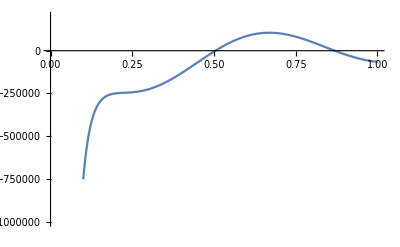

```mathematica
k=2π/λ;
Plot[(*1/(4 π)((Cos[k r]+Cos[√2 k r]/(√2))/r-(+Sin[k r]+Sin[√2 k r]/(2 π))/(k r^2)-(Cos[k r]-Cos[√2 k r]/(8 √2))/(k^2 r^3))/.r-> α λ*)ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]],{α,0.1,1},PlotRange->{-10^6,200000}]
```

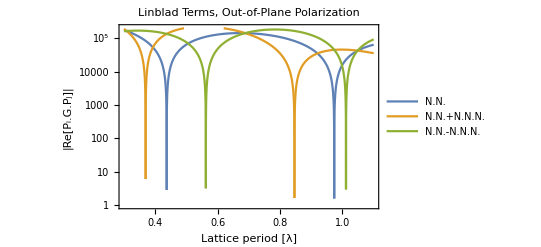

```mathematica
plt = LogPlot[{Abs[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],Abs[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]+ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]]],Abs[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]-ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]]]},{α,0.3,1.1},PlotStyle->Thin,PlotRange->{1,200000},PlotPoints->5000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Re[P_i.G.P_j]|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLegends->{"N.N.","N.N.+N.N.N.", "N.N.-N.N.N."}, PlotLabel->Style["Linblad Terms, Out-of-Plane Polarization",FontSize->12]]
```

```mathematica
(*Export["plot_nn_nnn_sqgrid_coupling.png",plt]*)
```

plot_nn_nnn_sqgrid_coupling.png

```mathematica
LogPlot[Abs[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","Re[P_i.G.P_j]"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

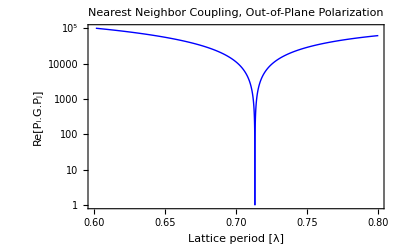

```mathematica
LogPlot[Abs[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","Re[P_i.G.P_j]"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

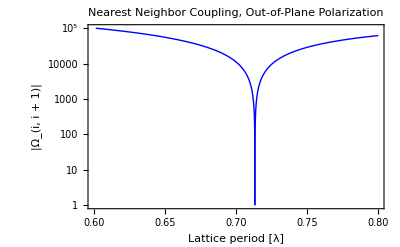

```mathematica
LogPlot[Abs[1/(4 π r)(Cos[k r](1-1/(k^2 r^2))-Sin[k r]/(k r))/.r-> α λ],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Ω_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

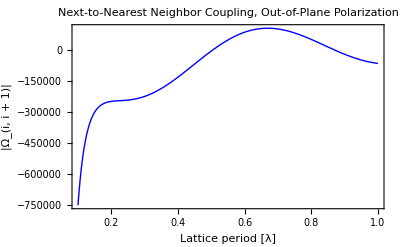

```mathematica
Plot[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]],{α,0.1,1},PlotStyle-> Directive[Blue,Thin],(*PlotRange->{1,100000},*)(*PlotPoints->3000,*)Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Ω_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Next-to-Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

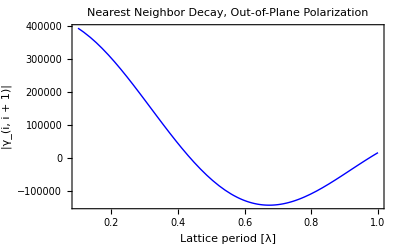

```mathematica
Plot[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]],{α,0.1,1},PlotStyle-> Directive[Blue,Thin],PlotRange->All(*PlotPoints->3000*),Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|γ_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Decay, Out-of-Plane Polarization",FontSize->12]]
```

```mathematica
Clear[k];
ComplexExpand[{1,0,0}.GdotP[{rx,ry,rz},{1,0,0}]]
```

(3 rx^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 k^2 π (rx^2+ry^2+rz^2)^(5/2))-Cos[k √(rx^2+ry^2+rz^2)]/(4 k^2 π (rx^2+ry^2+rz^2)^(3/2))+(ry^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2))+(rz^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2))+(3 rx^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 k π (rx^2+ry^2+rz^2)^2)-Sin[k √(rx^2+ry^2+rz^2)]/(4 k π (rx^2+ry^2+rz^2))+ⅈ (-(3 rx^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 k π (rx^2+ry^2+rz^2)^2)+Cos[k √(rx^2+ry^2+rz^2)]/(4 k π (rx^2+ry^2+rz^2))+(3 rx^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 k^2 π (rx^2+ry^2+rz^2)^(5/2))-Sin[k √(rx^2+ry^2+rz^2)]/(4 k^2 π (rx^2+ry^2+rz^2)^(3/2))+(ry^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2))+(rz^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2)))

```mathematica
Together[]
```

Why does the ferromagnetic mode become increasingly subradiant as d becomes smaller, whereas the nearest neighbor coupling vanishes very sharply?

#### Field polarization

```mathematica
GdotP[{1,1,0.01}scl,λ d{1,0,0}]
```

{0.00507646-0.0158561 ⅈ,-0.0102094+0.013154 ⅈ,-0.000102094+0.00013154 ⅈ}

## tests

Check my grid mapping. 2D grid, but only one index to specify atoms.

#### square grid

```mathematica
(*atomnum = 25;*)
num = √atomnum; 
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
gridpts = Table[atom[i,False],{i,Range[num^2]}];
(*excited= Table[atom[i,True],{i,Flatten@Table[(atomnum-1)/2+√atomnum i+j-1,{i,{-1,0,1}},{j,{-1,0,1}}]}];*)
positions[pts_]:=Table[r[1,j],{j,pts}]
```

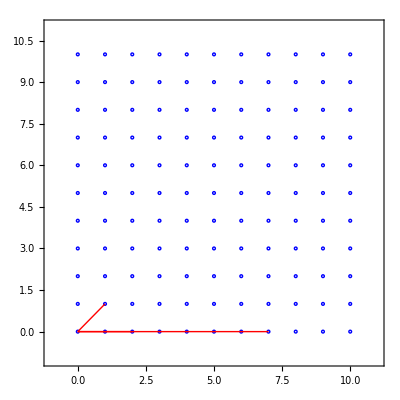

```mathematica
a=1;(*0.7;*)
showpos = {3,8,13};
Show[gridpts,positions[showpos],PlotRange->{{-a,a num},{-a,a num}},Frame->{True,True,False,False},Axes->False]
```

grid with defects

```mathematica
filling =0.7; 
defects=atomnum-Floor[filling atomnum+0.5];
(*remove some atoms from the system*)
atomIcds = Range[atomnum];
For[i=0,i<defects,i++,
rand = RandomChoice[atomIcds];
atomIcds= Select[atomIcds,#≠rand&];
];
```

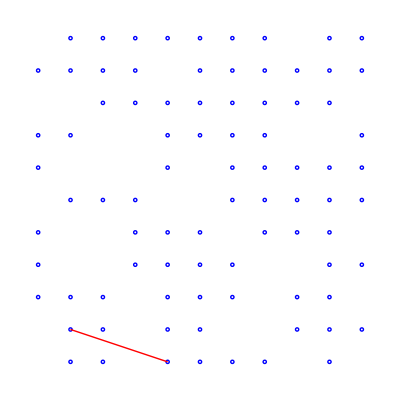

```mathematica
gridpts = Table[atom[i,False],{i,atomIcds}];
Show[gridpts,r[atomIcds[[3]],atomIcds[[8]]]]
```

#### hex grid

```mathematica
atomnumx=5;
atomnumy =Floor[2/(√3)atomnumx+0.5]; 
a=1;
x[i_]:=Mod[i-1,atomnumx]+a/2 Mod[Floor[(i-1)/atomnumx],2];
y[i_]:=(√3)/2 Floor[(i-1)/atomnumx];
Subscript[r, i_,j_]={0,Mod[j-1,atomnumx]-Mod[i-1,atomnumx]+a/2(Mod[Floor[(j-1)/atomnumx],2]-Mod[Floor[(i-1)/atomnumx],2]),(√3)/2(Floor[(j-1)/atomnumx]-Floor[(i-1)/atomnumx])};
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{x[i],y[i]},0.05]}],Graphics[{Blue,Circle[a{x[i],y[i]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{x[i],y[i]},a{x[j],y[j]}}]}];
gridpts = Table[atom[i,False],{i,Range[atomnumx atomnumy]}];
positions[pts_]:=Table[r[1,j],{j,pts}];
```

```mathematica
Table[Mod[Floor[(i-1)/atomnumx],2],{i,Range[atomnumx atomnumy]}]
```

{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1}

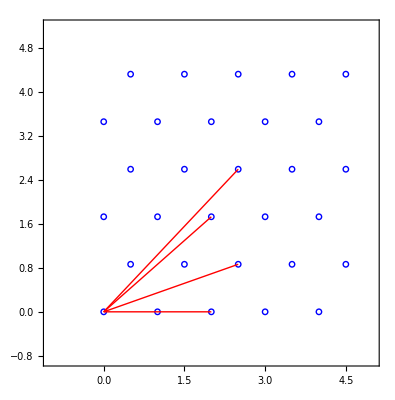

```mathematica
showpos = {3,8,13,18};
Show[gridpts,positions[showpos],PlotRange->{a{-1,atomnumx },a(√3)/2{-1,atomnumy}},Frame->{True,True,False,False},Axes->False]
```

```mathematica
Subscript[r, i_,j_]={0,Mod[j-1,atomnumx]-Mod[i-1,atomnumx]+a/2(Mod[Floor[(j-1)/atomnumx],2]-Mod[Floor[(i-1)/atomnumx],2]),(√3)/2(Floor[(j-1)/atomnumx]-Floor[(i-1)/atomnumx])};
```